# Zadanie 10 - Geneticky algoritmus

## 1. Stvorec [0,1] x [0,1]

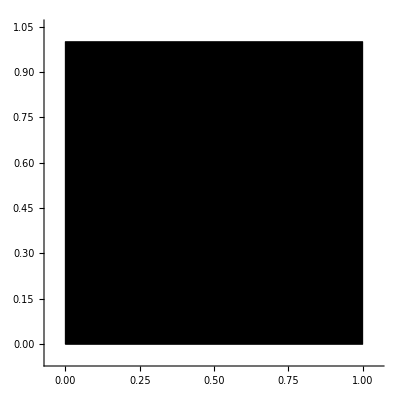

```mathematica
square = Graphics[{
   EdgeForm[Black],
   Rectangle[{0, 0}, {1, 1}]
   },
  Axes -> True,
  PlotRange -> {{-0.05, 1.05}, {-0.05, 1.05}}
];
Show[square]
```

## 2. n nahodnych bodov v stvorci

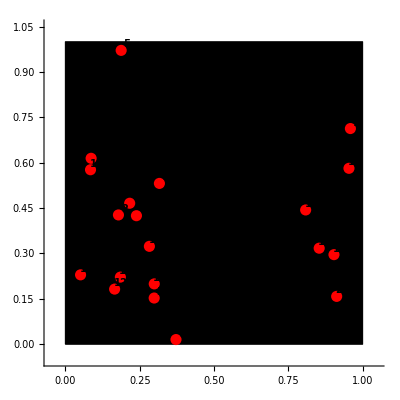

```mathematica
SeedRandom[15];
n = 20;
points = RandomReal[{0, 1}, {n, 2}];

plotPoints = Graphics[{
   PointSize[0.02], Red, Point /@ points,
   Black,
   MapIndexed[
    Text[Style[#2[[1]], 10, Bold], #1 + {0.02, 0.02}] &,
    points
   ]
}];
Show[square, plotPoints]
```

## 3. Pociatocna nahodna permutacia

x0 je nahodna permutacia 1..n. Funkcia pathGraphics nakresli cestu zodpovedajucu permutacii.

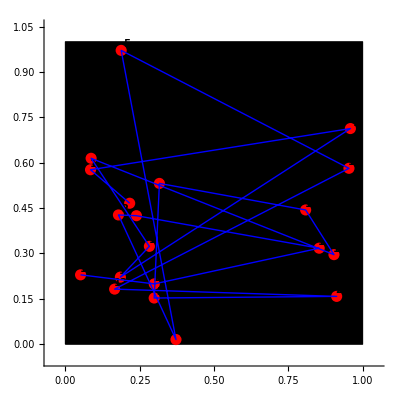

```mathematica
x0 = RandomSample[Range[n]];
pathGraphics[x_] := Graphics[{
   Blue, Thick, Line[points[[x]]]
}];
Show[square, plotPoints, pathGraphics[x0]]
```

## 4. Matica vzdialenosti L a ucelova funkcia f(x)

Maticu L vypocitame raz na zaciatku. Dlzka cesty f(x) sa potom pocita len sucitanim spravnych prvkov L (rychlejsie nez opakovane volania EuclideanDistance).
Cesta je OTVORENA, takze sumacia ide od k=1 po n-1.

```mathematica
L = Table[
	
   EuclideanDistance[points[[i]], points[[j]]],
   {i, n}, {j, n}
];
f[x_] := Sum[L[[x[[k]], x[[k + 1]]]], {k, 1, Length[x] - 1}];

f[x0]
```

10.4341

## 5. Stochasticke operatory poruchy

```mathematica
(* (a) Vymena dvoch susednych bodov. *)
neighbourA[x_] := Module[{xn = x, i},
  i = RandomInteger[{1, Length[x] - 1}];
  {xn[[i]], xn[[i + 1]]} = {xn[[i + 1]], xn[[i]]};
  xn
];

(* (b) Vymena lubovolnych dvoch bodov.*)
neighbourB[x_] := Module[{xn = x, i, j},
  {i, j} = RandomSample[Range[Length[x]], 2];
  {xn[[i]], xn[[j]]} = {xn[[j]], xn[[i]]};
  xn
];

(* (c) Prevratenie cesty medzi lubovolnymi dvoma bodmi. *)
neighbourC[x_] := Module[{xn = x, i, j},
  {i, j} = Sort[RandomSample[Range[Length[x]], 2]];
  xn[[i ;; j]] = Reverse[xn[[i ;; j]]];
  xn
];
```

## 8. Metropolisovo kriterium P(df, T)

Pre df<=0 vrati 1 (lepsi krok prijmeme vzdy). Pre df>0 exponencialne klesa s rastucim df a klesa pri klesajucom T.

```mathematica
P[df_, T_] := Min[1, Exp[-df/T]];

Manipulate[
  Plot[P[df, T], {df, -1, 1},
    AxesLabel -> {"df", "P"},
    PlotLabel -> Row[{"T = ", T}]
  ],
  {{T, 0.1}, 0.001, 1}
]
```

## 9. Algoritmus na hladanie vhodneho T0

Cielom je take T0, ze sa prijima asi 50% "horsich" stavov.
Z Metropolisa: priemerna pravdepodobnost prijatia horsieho stavu je priblizne Exp[-<df+>/T], kde <df+> je priemer kladnych df cez nahodnu prechadzku.
Riesime Exp[-<df+>/T0] = 0.5  =>  T0 = -<df+>/Log[0.5] = <df+>/Log[2].

```mathematica
findT0[x0_, neighbour_, samples_: 1000] := Module[
  {x = x0, xnew, df, dfList = {}},
  Do[
    xnew = neighbour[x];
    df = f[xnew] - f[x];
    If[df > 0, AppendTo[dfList, df]];
    x = xnew,
    {samples}
  ];
  -Mean[dfList]/Log[0.5]
];
```

Pred dalsim spustenim resetneme data na povodnych n=20 (pre pripad, ze ste spustili sekciu 7).

```mathematica
SeedRandom[42];
n = 20;
points = RandomReal[{0, 1}, {n, 2}];
L = Table[
   EuclideanDistance[points[[i]], points[[j]]],
   {i, n}, {j, n}];
x0 = RandomSample[Range[n]];
plotPoints = Graphics[{
   PointSize[0.02], Red, Point /@ points,
   Black,
   MapIndexed[
    Text[Style[#2[[1]], 10, Bold], #1 + {0.02, 0.02}] &,
    points
   ]
}];

T0auto = findT0[x0, neighbourC]
```

0.412472

## 10. Geneticky algoritmus a simulovane zihanie

Hlavny algoritmus. Vracia historiu (cesta, teplota, hodnota f) pre kazdu iteraciu - potrebne pre vizualizaciu.

```mathematica
simulatedAnnealing[x0_, T0_, alpha_, Tmin_, kmax_, neighbour_] := Module[
  {x = x0, T = T0, xnew, df,
   history = {{x0, T0, f[x0]}}},
  While[T > Tmin,
    Do[
      xnew = neighbour[x];
      df = f[xnew] - f[x];
      If[P[df, T] >= RandomReal[], x = xnew];
      AppendTo[history, {x, T, f[x]}],
      {kmax}
    ];
    T = alpha*T;
  ];
  history
];
```

```mathematica
orderCrossover[p1_,p2_]:=Module[{m=Length[p1],i,j,seg,rest},{i,j}=Sort[RandomSample[Range[m],2]];
seg=p1[[i;;j]];
rest=Select[p2,!MemberQ[seg,#]&];
Join[rest[[1;;i-1]],seg,rest[[i;;]]]];
tournamentSelect[population_,fvals_,tournSize_:3]:=Module[{idx},
idx=RandomSample[Range[Length[population]],tournSize];
population[[idx[[First[Ordering[fvals[[idx]],1]]]]]]];
geneticAlgorithm[popSize_,nCities_,nElite_,ngen_,Pm_,neighbour_,tournSize_:4, patience_]:=
Module[{pop,fvals,eliteIdx,newPop,p1,p2,child,bestIdx,history,noImprove=0,prevBest},
pop=Table[RandomSample[Range[nCities]],{popSize}];
fvals=f/@pop;
bestIdx=First[Ordering[fvals,1]];
history={{pop[[bestIdx]],1,fvals[[bestIdx]],Mean[fvals]}};
prevBest=fvals[[bestIdx]];
Do[eliteIdx=Ordering[fvals,nElite];
newPop=pop[[eliteIdx]];
While[Length[newPop]<popSize,p1=tournamentSelect[pop,fvals,tournSize];
p2=tournamentSelect[pop,fvals,tournSize];
child=orderCrossover[p1,p2];
If[RandomReal[]<=Pm,child=neighbour[child]];
AppendTo[newPop,child];];
pop=newPop;
fvals=f/@pop;
bestIdx=First[Ordering[fvals,1]];
AppendTo[history,{pop[[bestIdx]],gen,fvals[[bestIdx]],Mean[fvals]}];
If[fvals[[bestIdx]]<prevBest,prevBest=fvals[[bestIdx]];noImprove=0,noImprove++];
If[noImprove>=patience,Break[]],{gen,2,ngen}];
history];
```

Generations : 70

Initial f   : 7.33306

Final   f   : 3.65462

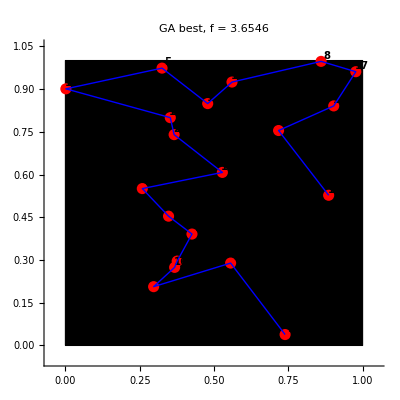

```mathematica
popSize=100;
nElite=20;
ngen=100;
Pm=0.3;
tournSz=4;

historyGA=geneticAlgorithm[popSize,n,nElite,ngen,Pm,neighbourC,tournSz, 20];

Print["Generations : ",Length[historyGA]];
Print["Initial f   : ",historyGA[[1,3]]];
Print["Final   f   : ",historyGA[[-1,3]]];
Show[square,plotPoints,pathGraphics[historyGA[[-1,1]]],PlotLabel->Row[{"GA best, f = ",NumberForm[historyGA[[-1,3]],{6,4}]}]]
```

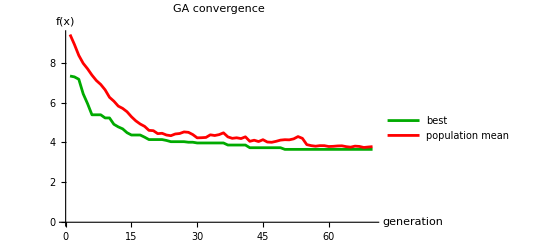

```mathematica
ListLinePlot[{historyGA[[All,3]],historyGA[[All,4]]},PlotLabel->"GA convergence",AxesLabel->{"generation","f(x)"},PlotLegends->{"best","population mean"},PlotStyle->{Darker[Green],Red}, PlotRange->All]
```

Generations : 40

Initial f   : 7.77582

Final   f   : 4.30878

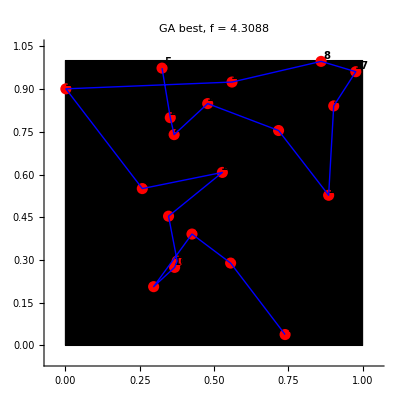

```mathematica
historyGAA=geneticAlgorithm[popSize,n,nElite,ngen,Pm,neighbourA,tournSz, 20];

Print["Generations : ",Length[historyGAA]];
Print["Initial f   : ",historyGAA[[1,3]]];
Print["Final   f   : ",historyGAA[[-1,3]]];
Show[square,plotPoints,pathGraphics[historyGAA[[-1,1]]],PlotLabel->Row[{"GA best, f = ",NumberForm[historyGAA[[-1,3]],{6,4}]}]]
```

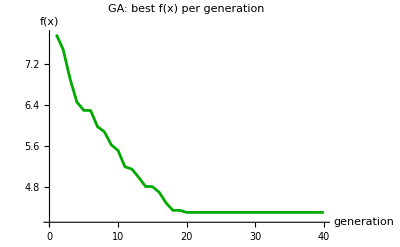

```mathematica
ListLinePlot[historyGAA[[All,3]],PlotLabel->"GA: best f(x) per generation",AxesLabel->{"generation","f(x)"},PlotStyle->Darker[Green]]
```

Generations : 53

Initial f   : 6.95786

Final   f   : 3.62889

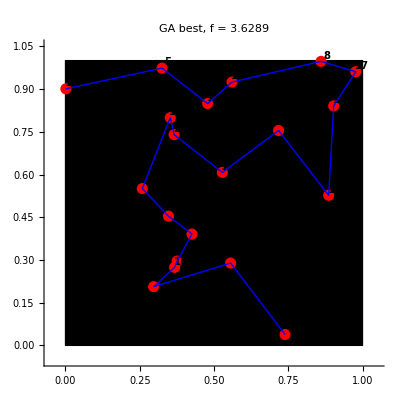

```mathematica
historyGAB=geneticAlgorithm[popSize,n,nElite,ngen,Pm,neighbourB,tournSz, 20];

Print["Generations : ",Length[historyGAB]];
Print["Initial f   : ",historyGAB[[1,3]]];
Print["Final   f   : ",historyGAB[[-1,3]]];
Show[square,plotPoints,pathGraphics[historyGAB[[-1,1]]],PlotLabel->Row[{"GA best, f = ",NumberForm[historyGAB[[-1,3]],{6,4}]}]]
```

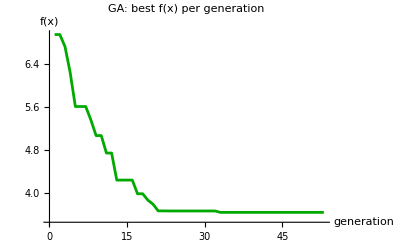

```mathematica
ListLinePlot[historyGAB[[All,3]],PlotLabel->"GA: best f(x) per generation",AxesLabel->{"generation","f(x)"},PlotStyle->Darker[Green]]
```

General::munfl: Exp[-724.03] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

# iter = 163001

f(xSA) = 4.90061

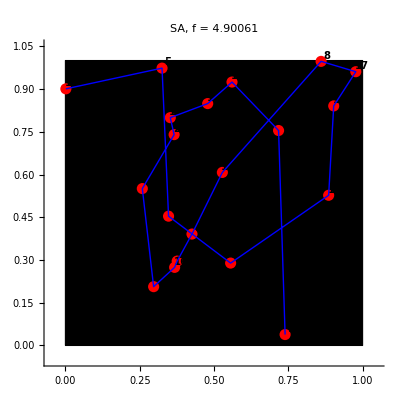

```mathematica
T0 = T0auto;
alpha = 0.95;
Tmin = 0.0001;
kmax = 1000;
history = simulatedAnnealing[x0, T0, alpha, Tmin, kmax, neighbourA];
Print["# iter = ", Length[history]];

xSA = history[[-1, 1]];
Print["f(xSA) = ", f[xSA]];
Show[square, plotPoints, pathGraphics[xSA],
 PlotLabel -> "SA, f = " <> ToString[f[xSA]]]
```

General::munfl: Exp[-740.931] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-717.381] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

# iter = 23601

f(xSA) = 3.65462

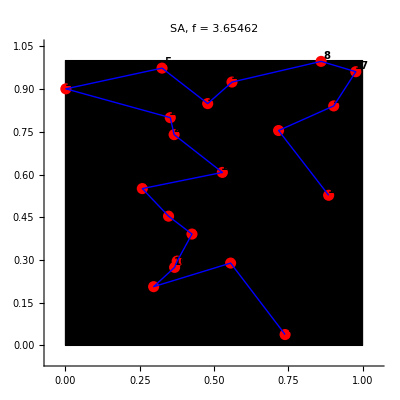

```mathematica
T0 = T0auto;
alpha = 0.95;
Tmin = 0.001;
kmax = 200;
history = simulatedAnnealing[x0, T0, alpha, Tmin, kmax, neighbourB];
Print["# iter = ", Length[history]];

xSA = history[[-1, 1]];
Print["f(xSA) = ", f[xSA]];
Show[square, plotPoints, pathGraphics[xSA],
 PlotLabel -> "SA, f = " <> ToString[f[xSA]]]
```

Spustenie SA. Operator (c) - reverse - dava najlepsie vysledky pre TSP (zodpoveda heuristike 2-opt).

General::munfl: Exp[-720.073] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-736.863] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

# iter = 23601

f(xSA) = 3.68156

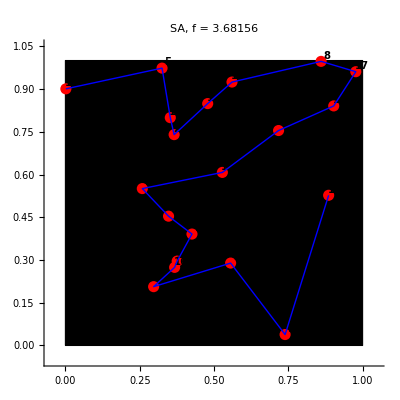

```mathematica
T0 = T0auto;
alpha = 0.95;
Tmin = 0.001;
kmax = 200;
history = simulatedAnnealing[x0, T0, alpha, Tmin, kmax, neighbourC];
Print["# iter = ", Length[history]];

xSA = history[[-1, 1]];
Print["f(xSA) = ", f[xSA]];
Show[square, plotPoints, pathGraphics[xSA],
 PlotLabel -> "SA, f = " <> ToString[f[xSA]]]
```

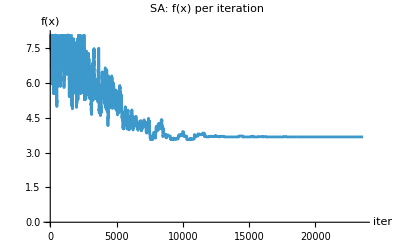

```mathematica
ListLinePlot[history[[All, 3]],
 PlotLabel -> "SA: f(x) per iteration",
 AxesLabel -> {"iter", "f(x)"}]
```

## 11. Vizualizacia algoritmu cez Manipulate

Posuvanim k prechadzame jednotlive iteracie. Zobrazujeme stvorec, body, aktualnu cestu, hodnotu f(x) a teplotu T.
Pri velkom pocte iteracii moze byt Manipulate pomaly - preto historiu zriedime.

```mathematica
step = Max[1, Floor[Length[history]/500]];
historyShort = history[[1 ;; -1 ;; step]];

Manipulate[
  Show[square, plotPoints,
    pathGraphics[historyShort[[k, 1]]],
    PlotLabel -> Row[{
      "iter ", k*step,
      ", T = ", NumberForm[historyShort[[k, 2]], {6, 4}],
      ", f(x) = ", NumberForm[historyShort[[k, 3]], {6, 4}]
    }]
  ],
  {k, 1, Length[historyShort], 1}
]
```

```mathematica
historyShortGA = historyGA[[1 ;; -1 ;; step]];

Manipulate[
  Show[square, plotPoints,
    pathGraphics[historyGA[[k, 1]]],
    PlotLabel -> Row[{
      "iter ", k,
      ", T = ", NumberForm[historyGA[[k, 2]], {6, 4}],
      ", f(x) = ", NumberForm[historyGA[[k, 3]], {6, 4}]
    }]
  ],
  {k, 1, Length[historyGA], 1}
]
```

```mathematica
historyShortGAB = historyGAB[[1 ;; -1 ;; step]];

Manipulate[
  Show[square, plotPoints,
    pathGraphics[historyGAB[[k, 1]]],
    PlotLabel -> Row[{
      "iter ", k,
      ", T = ", NumberForm[historyGAB[[k, 2]], {6, 4}],
      ", f(x) = ", NumberForm[historyGAB[[k, 3]], {6, 4}]
    }]
  ],
  {k, 1, Length[historyGAB], 1}
]
```

## 12. Porovnanie operatorov poruchy

Spustime SA viackrat pre kazdy z troch operatorov a vyhodnotime priemer, minimum a smerodajnu odchylku najdenej hodnoty f.

```mathematica
runs = 5;
compareOp[neighbour_] := Module[{results},
  results = Table[
    simulatedAnnealing[
      RandomSample[Range[n]],
      T0auto, 0.95, 0.0001, 100, neighbour
    ][[-1, 3]],
    {runs}
  ];
  {Mean[results], Min[results], StandardDeviation[results]}
];

Print["Operator (a) swap-neighbours    : ", compareOp[neighbourA]];
Print["Operator (b) swap-any-two       : ", compareOp[neighbourB]];
Print["Operator (c) reverse-sub-path   : ", compareOp[neighbourC]];
```

General::munfl: Exp[-712.917] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Operator (a) swap-neighbours    : {5.31852,4.84161,0.413927}

General::munfl: Exp[-820.976] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-739.913] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-778.856] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Operator (b) swap-any-two       : {3.90615,3.65462,0.17312}

General::munfl: Exp[-719.377] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-737.264] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-721.582] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Operator (c) reverse-sub-path   : {3.64978,3.5637,0.0488529}